```mathematica
ClearAll["Global`*"];
```

```mathematica
x1 = 0; x2=10;hmem=1;tb=5;μ=0; ϕ=0;
hp[t_, tb_]:=hmem HeavisideTheta[t-tb]
(*hp[t_, tb_]:=hmem Tanh[t-tb]*)
hc[t_, tb_]:=0
```

```mathematica
S[t_]:= 1/2(1+μ)(Integrate[hp[τ, tb], {τ, 0, t}]Cos[2 ϕ]+Integrate[hc[τ, tb], {τ, 0, t}]Sin[2 ϕ])
```

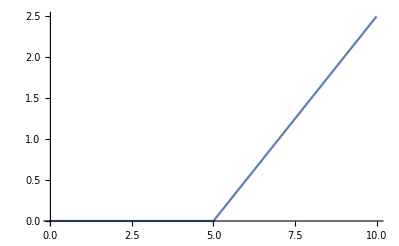

```mathematica
Plot[S[ x], {x, 0, 10}]
```

```mathematica
data=Transpose@{Range[0, 10, 0.05],Map[S, Range[0, 10, 0.05]]};
```

```mathematica
parabola=Fit[data,{1,x,x^2},x]
```

0.151643-0.216453 x+0.0466453 x^2

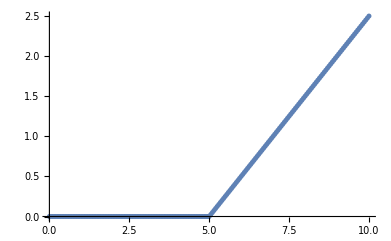

```mathematica
ListPlot[data]
```

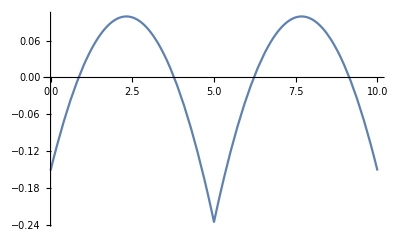

```mathematica
Plot[S[ x]-parabola, {x, 0, 10}]
```

```mathematica
FT[ω ]=Simplify[FourierTransform[S[ x]-parabola, x,ω ]Conjugate[FourierTransform[S[ x]-parabola, x,ω ]]//ComplexExpand]
```

(0.+0. ⅈ)+0.0397887/ω^4+(5.23789×10^-32)/ω^2

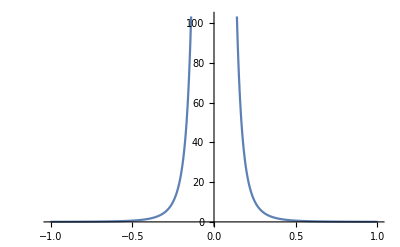

```mathematica
Plot[FT[ω], {ω, -1, 1}]
(*s[t_]:= Integrate[]*)
```